# Is the instantaneous Internet real?

Constantine Korikov

Spoiler: no.

*phrases in "red" show definitions, while those in ["blue"](https://en.wikipedia.org/wiki/Blue) are links to webpages.

## Intro

If we type an "URL" of any site in our favourite "web browser", we will get there pretty quickly. For instance, getting a response from ["https://wolfram.com"](https://wolfram.com) takes the following amount of seconds for the first byte.

```mathematica
URLResponseTime["https://wolfram.com"]
```

0.552851 s

Even though the "server" is located far enough, this response time is not dramatically long.

```mathematica
With[{A=,B=Here},GeoGraphics[{,,},]]
```

-Graphics-

This period can be roughly split into two parts : lag and data transmission.

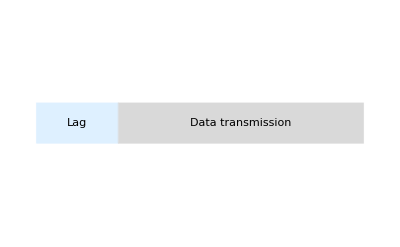

```mathematica
BarChart[{,},]
```

However, can this response be instantaneous? We already know the answer. No! It is impossible to transmit information so fast.

Let us look in the essay at some fundamental reasons which do not allow us to do it. In the following paragraphs, we will discuss several constraints from basic information theory and physics.

## Lag

The lag in the response time is due to the time required to establish a connection in the network.  In physics, the "theory of relativity" forbids instantaneous information transmission1. If that were allowed, it could lead to the violation of causality. That is why the theory postulates that the speed of information propagation cannot be more than the fixed value, which equals to "speed of light".

```mathematica
Entity["PhysicalConstant","SpeedOfLight"][EntityProperty["PhysicalConstant","Value"]]
```

299792458 m/s

If it travels through the medium then the speed of light becomes less and can be calculated by dividing the speed of light in the "vacuum" c on the "refractive index" n.

ν=c/n

It is important to note that "quantum entanglement" does not help to avoid restrictions on instantaneous information transmission. The ["no-communication theorem"](https://en.wikipedia.org/wiki/No-communication_theorem) states this2. For example, in experiments involving "quantum teleportation", where quantum entanglement is exploited, it is required a classical "channel" to send information, which in turn is restricted with the limit of the speed of light. But quantum entanglement can be used for "superdense coding" of the information that increases the data rate. The data transmission phase of response is discussed below.

## Data transmission

Time of data transmission mainly depends on the data rate and many factors affect it. Let us look at some of them.

### Numeration system

The data rate is measured in bits per seconds. A bit is a unit of information, which was chosen because it is closer to optimal encoding. The optimal "radix" r for a "numeration system" can be found differently. One way is a minimisation of the size of the alphabet and the length w=N log_r of words together, where N represents the number of states of some entity3.

log_r(N)r

If we plot this value for different bases, we can see that there is an optimal point.

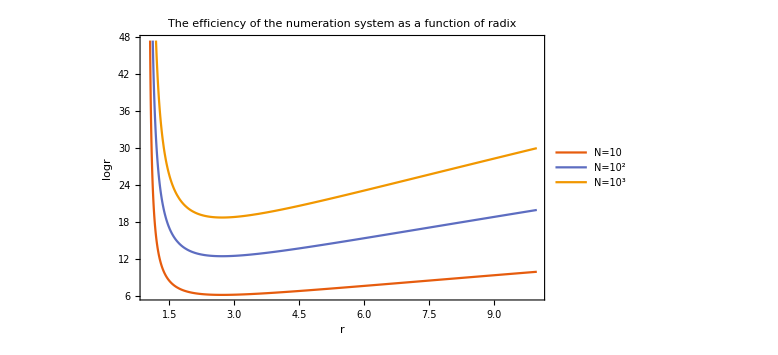

```mathematica
Plot[{Subscript[log, r](10)r,Subscript[log, r](10^2)r,Subscript[log, r](10^3)r},{r,1,10},]
```

The point can be found analytically.

```mathematica
Solve[(∂(Subscript[log, r](N)r))/(∂r)==0,r]
```

{{r→ⅇ}}

The answer shows that it is an exponent. The nearest integer values are 2 (bits) and 3 (trits).

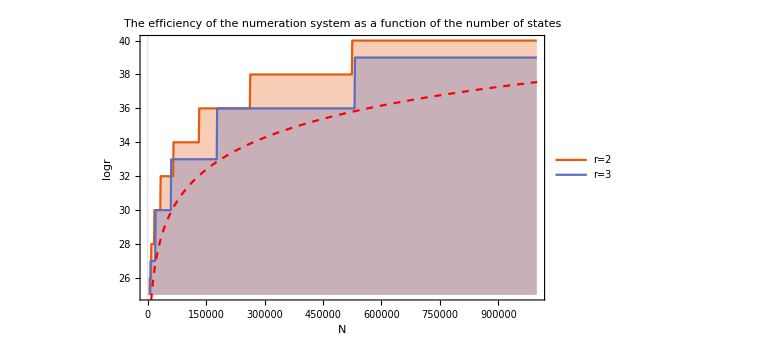

```mathematica
Show[ListPlot[Function[r,{#,r Total[DigitCount[#,r]]}&/@Range[1,10^6,10^3]]/@{2,3},],Plot[Log[x] ⅇ,{x,1,10^6},]]
```

On the above picture, we can see that trits are more efficient than bits, but from a technical point of view usage of bits is easier. For both integer bases, the divergence from optimal values decreases the effectiveness of the numeration system. As a result, it decreases the data rate.

### Influence of noise

Because the information is transmitted in the real world, the signal is exposed to "noises". ["Shannon–Hartley theorem"](https://en.wikipedia.org/wiki/Shannon%E2%80%93Hartley_theorem) states that there is the theoretical maximum rate at which information can be transmitted over a communications channel in the presence of noise4.

The theorem is formulated in the language of spectra. It is a useful mathematical representation which physically corresponds to the fact that any real "signal" can be represented as a sum of simple ones. Such representation can be performed with the help of the ["Fourier transform"](https://en.wikipedia.org/wiki/Fourier_transform).

For instance, the demonstration below shows "spectrogram" of an audio signal on the left side. On the right side, we can see the same signal but on the output of the channel. Here, the channel behaves like a low pass filter. In other words, it suppresses higher components of the spectrum of the signal. In the demo, the signal can be shifted (Δf), and the cutoff frequency (ω_c) of the channel can be tuned.

```mathematica
Manipulate[audio=AudioFrequencyShift[ExampleData[{"Audio","Piano"}],Quantity[f,"Hertz"]];filtered=LowpassFilter[audio,Quantity[w,"Hertz"]];
Row@{If[view,Spectrogram[audio,ImageSize->Medium],audio],If[view,Spectrogram[filtered,ImageSize->Medium],filtered]},
{{f,0,"Δf"},0,3000,1000},{{w,5000,"f_c"},0,5000,500},{{view,True,"Spectrum"},{True,False}},ContinuousAction->False
]
```

In the language of the spectra, the "channel capacity" in bits per second with a presence of ["additive white Gaussian noise"](https://en.wikipedia.org/wiki/Additive_white_Gaussian_noise) can be written as follows.

C=B log_2(1+S/N)

Here B is the maximum spectrum width of the signal, which can be transmitted through the channel, and S/N is a "signal-to-noise ratio".

Introducing the W as the width of the band where S = N, we can see the useful dependence for normalised channel capacity.

```mathematica
Manipulate[Plot[ B/W Log[2,1+W/B],{B,0,10^6},],{{W,10^5,"W, Hz"},10^4,10^6}]
```

As we can see, as we increase the band, the capacity increases until the value where the total noise power is about equal to the signal power. In the result, we can make sure that the data rate is also limited due to noises.

### Formats

Additionally, formats of data reduce data rate because they add extra information. For instance, to encode a text in the English dictionary it is required only the following amount of bits.

```mathematica
Quantity[Log[2,Length@Alphabet[]],"Bits"]//N
```

4.70044 b

The nearest higher integer is 5 and this 5-bit code can encode 2^5 = 32 symbols. It is more than required. In practice, it is used longer codes like "ASCII"5. The table is shown below.

```mathematica
Multicolumn[Labeled[BaseForm[#,2],FromCharacterCode[#],LabelStyle->RGBColor[Rational[212, 255], 0, Rational[4, 51]]]&/@Range[0,127],12, ]
```

0_2.00 | 1_2.01 | 10_2.02 | 11_2.03 | 100_2.04 | 101_2.05 | 110_2.06 | 111_2.07 | 1000_2.08 | 1001_2	 | 1010_2
 | 1011_2.0b
1100_2\f | 1101_2\r | 1110_2.0e | 1111_2.0f | 10000_2.10 | 10001_2.11 | 10010_2.12 | 10011_2.13 | 10100_2.14 | 10101_2.15 | 10110_2.16 | 10111_2.17
11000_2.18 | 11001_2.19 | 11010_2.1a | 11011_2 | 11100_2.1c | 11101_2.1d | 11110_2.1e | 11111_2.1f | 100000_2  | 100001_2! | 100010_2" | 100011_2#
100100_2$ | 100101_2% | 100110_2& | 100111_2' | 101000_2( | 101001_2) | 101010_2* | 101011_2+ | 101100_2, | 101101_2- | 101110_2. | 101111_2/
110000_20 | 110001_21 | 110010_22 | 110011_23 | 110100_24 | 110101_25 | 110110_26 | 110111_27 | 111000_28 | 111001_29 | 111010_2: | 111011_2;
111100_2< | 111101_2= | 111110_2> | 111111_2? | 1000000_2@ | 1000001_2A | 1000010_2B | 1000011_2C | 1000100_2D | 1000101_2E | 1000110_2F | 1000111_2G
1001000_2H | 1001001_2I | 1001010_2J | 1001011_2K | 1001100_2L | 1001101_2M | 1001110_2N | 1001111_2O | 1010000_2P | 1010001_2Q | 1010010_2R | 1010011_2S
1010100_2T | 1010101_2U | 1010110_2V | 1010111_2W | 1011000_2X | 1011001_2Y | 1011010_2Z | 1011011_2[ | 1011100_2\ | 1011101_2] | 1011110_2^ | 1011111_2_
1100000_2` | 1100001_2a | 1100010_2b | 1100011_2c | 1100100_2d | 1100101_2e | 1100110_2f | 1100111_2g | 1101000_2h | 1101001_2i | 1101010_2j | 1101011_2k
1101100_2l | 1101101_2m | 1101110_2n | 1101111_2o | 1110000_2p | 1110001_2q | 1110010_2r | 1110011_2s | 1110100_2t | 1110101_2u | 1110110_2v | 1110111_2w
1111000_2x | 1111001_2y | 1111010_2z | 1111011_2{ | 1111100_2| | 1111101_2} | 1111110_2~ | 1111111_2.7f |  |  |  |

Redundant code space can be reduced, for example by ["entropic compression"](https://en.wikipedia.org/wiki/Entropy_encoding). To do this we can use "Huffman code". For instance, we can encode the string “wolfram mathematica” as follows. The binary length of the encoded string is shown below.

```mathematica
sizeCompressed=ResourceFunction["HuffmanEncode"]["wolfram mathematica"]["Encoding"]//Length
```

67

If we use 7-bit ASCII code,

```mathematica
sizeOneSymbolASCII=7;
```

we will get the following length of the string.

```mathematica
sizeOriginal=sizeOneSymbolASCII StringLength["wolfram mathematica"]
```

133

The ration of the sizes reveals the redundancy of the ASCII code.

```mathematica
sizeOriginal/sizeCompressed//N
```

1.98507

The idea behind the code is simple. The more often symbol in the text is the shorter code is used for it. In average, this representation requires less data to send the same amount of information. However, these methods fundamentally do not solve the problem of extra data due to format.

Thus, non-ideally numeration system, format redundancy and influence of noise cause the reduction of data rate.

## Conclusions

We considered in the essay the influence of some fundamental constraints on information transmission through the single data channel. Obviously, the Internet is a network, where every segment of the net is linked to each other with "commutators". Also, there are services that work in the network like "IP" protocol with "TCP" over it which are used by "HTTP" on the application layer6. In addition, there are protocols for resolving addresses like "DNS" and "ARP". Some of them we can see if we launch the process of getting the first byte from the site with details.

```mathematica
URLResponseTime["https://wolfram.com",All]//Dataset
```

Dataset[<>]

All these services take much more time than the effects considered here. In any case, even if we managed to get the time needed for those services to minimum,  we would still have to deal with all the theoretical limits discussed above.

## References

1	Landau, L. D. & Lifshitz, E. M. The Classical Theory of Fields: Volume 2. (Butterworth-Heinemann, 1980).

2	Peres, A. & Terno, D. R. Quantum information and relativity theory. Rev. Mod. Phys. 76, 93–123 (2004).

3	Hayes, B. Third Base. Am Sci 89, 488–492 (2001).

4	Shannon, C. E. Communication in the Presence of Noise. Proc. IRE 37, 10–21 (1949).

5	ASA standard X3.4. (1963).

6	Olifer, N. & Olifer, V. Computer Networks: Principles, Technologies and Protocols for Network Design. (Wiley, 2005).